```mathematica
Needs["PlotLegends`"]
```

```mathematica
v="9";
p="0.2";

g5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/GapD-l5k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/velD-l5k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/AveVel-l5k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number}];
g10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/GapD-l10k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/velD-l10k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/AveVel-l10k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number}];
g20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/GapD-l20k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/velD-l20k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/AveVel-l20k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number}];
g30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/GapD-l30k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/velD-l30k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/AveVel-l30k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number}];
g40k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/GapD-l40k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v40k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/velD-l40k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av40k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/AveVel-l40k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number}];
g50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/GapD-l50k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/velD-l50k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/AveVel-l50k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number}];
ngap="3";
nvel="4";
jj=StringToStream[ngap];
ng= Read[jj,Number];
ii=StringToStream[nvel];
nv= Read[ii,Number];
ClearAll[d0,z,α];
d0=0.0674;
z=0.65;
α=0.65;
gap5v9=Table[{g5k1[[All,1]][[j]],Sum[g5k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g5k1]}];
vel5v9=Table[{v5k1[[All,1]][[j]],Sum[v5k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v5k1]}];
avel5v9=Table[{av5k1[[All,1]][[j]],av5k1[[All,2]][[j]]},{j,1,Length[av5k1]}];
gap10v9=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g10k1]}];
vel10v9=Table[{v10k1[[All,1]][[j]],Sum[v10k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v10k1]}];
avel10v9=Table[{av10k1[[All,1]][[j]],av10k1[[All,2]][[j]]},{j,1,Length[av10k1]}];
gap20v9=Table[{g20k1[[All,1]][[j]],Sum[g20k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g20k1]}];
vel20v9=Table[{v20k1[[All,1]][[j]],Sum[v20k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v20k1]}];
avel20v9=Table[{av20k1[[All,1]][[j]],av20k1[[All,2]][[j]]},{j,1,Length[av20k1]}];
gap30v9=Table[{g30k1[[All,1]][[j]],Sum[g30k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g30k1]}];
vel30v9=Table[{v30k1[[All,1]][[j]],Sum[v30k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v30k1]}];
avel30v9=Table[{av30k1[[All,1]][[j]],av30k1[[All,2]][[j]]},{j,1,Length[av30k1]}];
gap40v9=Table[{g40k1[[All,1]][[j]],Sum[g40k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g40k1]}];
vel40v9=Table[{v40k1[[All,1]][[j]],Sum[v40k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v40k1]}];
avel40v9=Table[{av40k1[[All,1]][[j]],av40k1[[All,2]][[j]]},{j,1,Length[av40k1]}];
gap50v9=Table[{g50k1[[All,1]][[j]],Sum[g50k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g50k1]}];
vel50v9=Table[{v50k1[[All,1]][[j]],Sum[v50k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v50k1]}];
avel50v9=Table[{av50k1[[All,1]][[j]],av50k1[[All,2]][[j]]},{j,1,Length[av50k1]}];
```

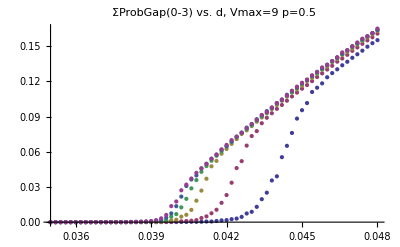

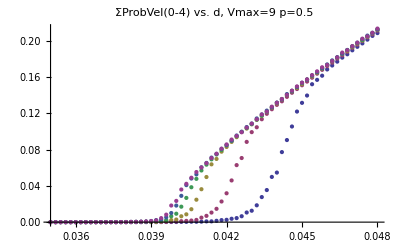

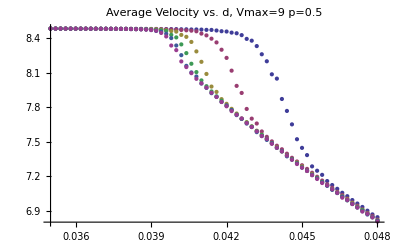

```mathematica
ListPlot[{gap5v9,gap10v9,gap20v9,gap30v9,gap40v9,gap50v9},PlotLabel->"ΣProbGap(0-"<>ngap<>") vs. d, Vmax="<>v<>"  p="<>p,PlotLegend->{"5k","10k","20k","30k","40k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None]
ListPlot[{vel5v9,vel10v9,vel20v9,vel30v9,vel40v9,vel50v9},PlotLabel->"ΣProbVel(0-"<>nvel<>") vs. d, Vmax="<>v<>"  p="<>p,PlotLegend->{"5k","10k","20k","30k","40k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None]
ListPlot[{avel5v9,avel10v9,avel20v9,avel30v9,avel40v9,avel50v9},PlotLabel->"Average Velocity vs. d, Vmax="<>v<>"  p="<>p,PlotRange->Full,PlotLegend->{"5k","10k","20k","30k","40k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None]
```

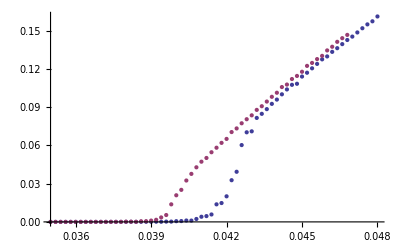

```mathematica
ListPlot[{gap10v9,gap50v9}]
```

0.0358

0.25

0.25

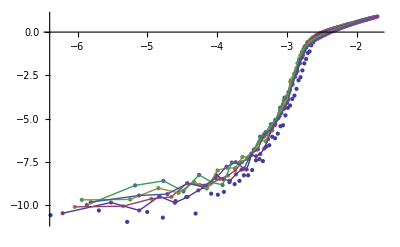

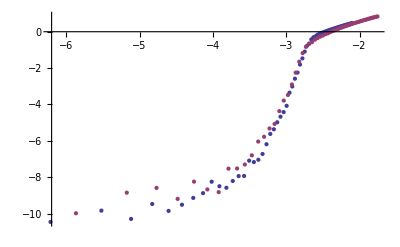

```mathematica
ClearAll[d0,z,α];
d0=0.0358;
α=0.25;
z=0.25;

ga5k1=gap5v9[[All,1]];
ga10k1=gap10v9[[All,1]];
ga20k1=gap20v9[[All,1]];
ga30k1=gap30v9[[All,1]];
ga40k1=gap40v9[[All,1]];
ga50k1=gap50v9[[All,1]];

ga5k2=gap5v9[[All,2]];
ga10k2=gap10v9[[All,2]];
ga20k2=gap20v9[[All,2]];
ga30k2=gap30v9[[All,2]];
ga40k2=gap40v9[[All,2]];
ga50k2=gap50v9[[All,2]];

g5k=Table[{Log[ga5k1[[i]]-d0]+z*Log[5*1000.],
Log[ga5k2[[i]]]+α*Log[5*1000.]},{i,1,Length[ga5k1]}];
g10k=Table[{Log[ga10k1[[i]]-d0]+z*Log[10*1000.],
Log[ga10k2[[i]]]+α*Log[10*1000.]},{i,1,Length[ga10k1]}];

g20k=Table[{Log[ga20k1[[i]]-d0]+z*Log[20*1000.],Log[ga20k2[[i]]]+α*Log[20*1000.]},{i,1,Length[ga20k1]}];
g30k=Table[{Log[ga30k1[[i]]-d0]+z*Log[30*1000.],Log[ga30k2[[i]]]+α*Log[30*1000.]},{i,1,Length[ga30k1]}];
g40k=Table[{Log[ga40k1[[i]]-d0]+z*Log[40*1000.],Log[ga40k2[[i]]]+α*Log[40*1000.]},{i,1,Length[ga40k1]}];
g50k=Table[{Log[ga50k1[[i]]-d0]+z*Log[50*1000.],Log[ga50k2[[i]]]+α*Log[50*1000.]},{i,1,Length[ga50k1]}];
pic5=ListPlot[{g5k,g10k,g20k,g30k,g40k,g50k},PlotRange->Full];
pic6=ListLinePlot[{g10k,g20k,g30k,g40k,g50k},PlotRange->Full];
d0
z
α
Show[{pic5,pic6}]
ListPlot[{g10k,g40k}]
```

1.44497  = val

0.0358  = d0

0.25  = α

0.25  = z

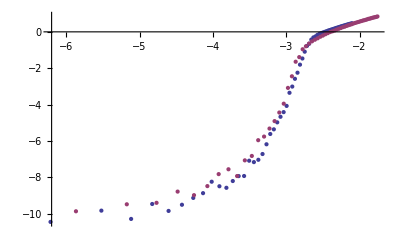

```mathematica
ga10k1=gap10v9[[All,1]];
ga50k1=gap50v9[[All,1]];
ga10k2=gap10v9[[All,2]];
ga50k2=gap50v9[[All,2]];
val=1000;
For[d0=0.035,d0<=0.04,d0+=0.0001,
For[α=0.01,α≤0.8,α+=0.01,
z=α;
j=1;
While[ga10k1[[j]]<=d0,j++];
k=1;
While[ga50k1[[k]]<=d0,k++];
g10k=Table[{Log[ga10k1[[i]]-d0]+z*Log[10*1000.],
Log[ga10k2[[i]]]+α*Log[10*1000.]},{i,j,Length[ga10k1]-1}];
g50k=Table[{Log[ga50k1[[i]]-d0]+z*Log[50*1000.],Log[ga50k2[[i]]]+α*Log[50*1000.]},{i,k,Length[ga50k1]-1}];
i10=Interpolation[g10k];
i50=Interpolation[g50k];
min=Max[Log[ga10k1[[j]]-d0]+z*Log[10*1000.],Log[ga50k1[[k]]-d0]+z*Log[50*1000.]];
max=Min[Log[ga10k1[[Length[ga10k1]-1]]-d0]+z*Log[10*1000.],Log[ga50k1[[Length[ga50k1]-1]]-d0]+z*Log[50*1000.]];
delta=(max-min)/50;
int=Sum[delta*(Max[i10[min+k*delta],i50[min+k*delta]]-Min[i10[min+k*delta],i50[min+k*delta]]),{k,0,50}];
If[int<val,
val=int;
d0f=d0;
αf=α;
zf=z;]

]
]


" = val"  val
" = d0" d0f
" = α" αf
" = z" zf
g10k=Table[{Log[ga10k1[[i]]-d0f]+zf*Log[10*1000.],
Log[ga10k2[[i]]]+αf*Log[10*1000.]},{i,1,Length[ga10k1]}];
g50k=Table[{Log[ga50k1[[i]]-d0f]+zf*Log[40*1000.],Log[ga50k2[[i]]]+αf*Log[40*1000.]},{i,1,Length[ga50k1]}];
ListPlot[{g10k,g50k}]
```

0.358  = d0

0.25  = α

0.25  = z

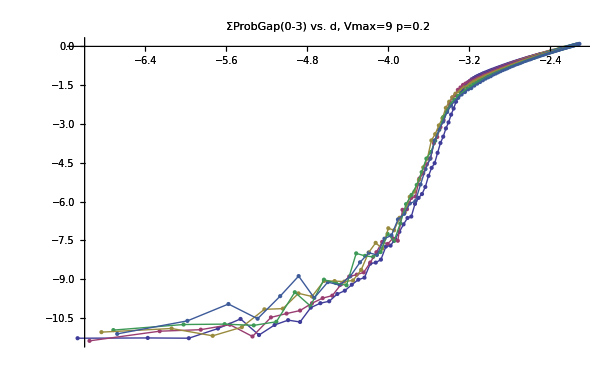

```mathematica
d0=0.358;
α=0.25;
z=0.25;
ga5k1=gap5v9[[All,1]];
ga10k1=gap10v9[[All,1]];
ga20k1=gap20v9[[All,1]];
ga40k1=gap40v9[[All,1]];
ga50k1=gap50v9[[All,1]];
ga5k2=gap5v9[[All,2]];
ga10k2=gap10v9[[All,2]];
ga20k2=gap20v9[[All,2]];
ga40k2=gap40v9[[All,2]];
ga50k2=gap50v9[[All,2]];
g5k=Table[{Log[ga5k1[[i]]-d0f]+zf*Log[5*1000.],
Log[ga5k2[[i]]]+αf*Log[5*1000.]},{i,1,Length[ga5k1]}];
g10k=Table[{Log[ga10k1[[i]]-d0f]+zf*Log[10*1000.],
Log[ga10k2[[i]]]+αf*Log[10*1000.]},{i,1,Length[ga10k1]}];
g20k=Table[{Log[ga20k1[[i]]-d0f]+zf*Log[20*1000.],
Log[ga20k2[[i]]]+αf*Log[20*1000.]},{i,1,Length[ga20k1]}];
g40k=Table[{Log[ga40k1[[i]]-d0f]+zf*Log[40*1000.],
Log[ga40k2[[i]]]+αf*Log[40*1000.]},{i,1,Length[ga40k1]}];
g50k=Table[{Log[ga50k1[[i]]-d0f]+zf*Log[50*1000.],Log[ga50k2[[i]]]+αf*Log[50*1000.]},{i,1,Length[ga50k1]}];
pic1=ListPlot[{g5k,g10k,g20k,g40k,g50k},PlotLabel->"ΣProbGap(0-"<>ngap<>") vs. d, Vmax="<>v<>"  p="<>p,PlotLegend->{"5k","10k","20k","40k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None];
pic2=ListLinePlot[{g5k,g10k,g20k,g40k,g50k},PlotLabel->"ΣProbGap(0-"<>ngap<>") vs. d, Vmax="<>v<>"  p="<>p,PlotLegend->{"5k","10k","20k","40k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None];
" = d0" d0
" = α" α
" = z" z
Show[{pic1,pic2}]
```

```mathematica
------------------------------------------------------------------------------------------
```

```mathematica
v="9";
p="0.2";

g5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/GapD-l5k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/velD-l5k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/AveVel-l5k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number}];
g10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/GapD-l10k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/velD-l10k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/AveVel-l10k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number}];
g20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/GapD-l20k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/velD-l20k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/AveVel-l20k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number}];
g40k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/GapD-l40k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v40k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/velD-l40k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av40k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/AveVel-l40k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number}];
g50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/GapD-l50k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/velD-l50k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/testResults/AveVel-l50k-v"<>v<>"-p"<>p<>".txt",{Number,Number,Number,Number}];
ngap="3";
nvel="4";
jj=StringToStream[ngap];
ng= Read[jj,Number];
ii=StringToStream[nvel];
nv= Read[ii,Number];
ClearAll[d0,z,α];
d0=0.0674;
z=0.65;
α=0.65;
gap5v9=Table[{g5k1[[All,1]][[j]],Sum[g5k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g5k1]}];
vel5v9=Table[{v5k1[[All,1]][[j]],Sum[v5k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v5k1]}];
avel5v9=Table[{av5k1[[All,1]][[j]],av5k1[[All,2]][[j]]},{j,1,Length[av5k1]}];
gap10v9=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g10k1]}];
vel10v9=Table[{v10k1[[All,1]][[j]],Sum[v10k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v10k1]}];
avel10v9=Table[{av10k1[[All,1]][[j]],av10k1[[All,2]][[j]]},{j,1,Length[av10k1]}];
gap20v9=Table[{g20k1[[All,1]][[j]],Sum[g20k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g20k1]}];
vel20v9=Table[{v20k1[[All,1]][[j]],Sum[v20k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v20k1]}];
avel20v9=Table[{av20k1[[All,1]][[j]],av20k1[[All,2]][[j]]},{j,1,Length[av20k1]}];
gap30v9=Table[{g30k1[[All,1]][[j]],Sum[g30k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g30k1]}];
vel30v9=Table[{v30k1[[All,1]][[j]],Sum[v30k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v30k1]}];
avel30v9=Table[{av30k1[[All,1]][[j]],av30k1[[All,2]][[j]]},{j,1,Length[av30k1]}];
gap40v9=Table[{g40k1[[All,1]][[j]],Sum[g40k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g40k1]}];
vel40v9=Table[{v40k1[[All,1]][[j]],Sum[v40k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v40k1]}];
avel40v9=Table[{av40k1[[All,1]][[j]],av40k1[[All,2]][[j]]},{j,1,Length[av40k1]}];
gap50v9=Table[{g50k1[[All,1]][[j]],Sum[g50k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g50k1]}];
vel50v9=Table[{v50k1[[All,1]][[j]],Sum[v50k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v50k1]}];
avel50v9=Table[{av50k1[[All,1]][[j]],av50k1[[All,2]][[j]]},{j,1,Length[av50k1]}];
```

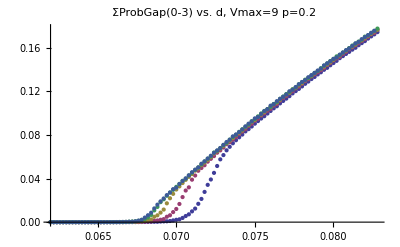

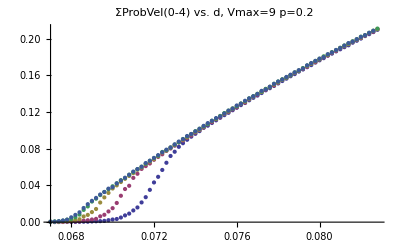

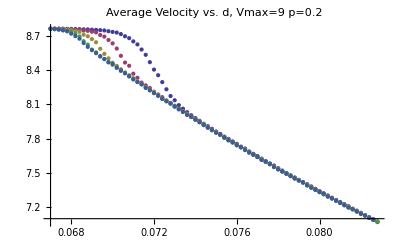

```mathematica
ListPlot[{gap5v9,gap10v9,gap20v9,gap40v9,gap50v9},PlotLabel->"ΣProbGap(0-"<>ngap<>") vs. d, Vmax="<>v<>"  p="<>p,PlotLegend->{"5k","10k","20k","40k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None]
ListPlot[{vel5v9,vel10v9,vel20v9,vel40v9,vel50v9},PlotLabel->"ΣProbVel(0-"<>nvel<>") vs. d, Vmax="<>v<>"  p="<>p,PlotLegend->{"5k","10k","20k","40k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None]
ListPlot[{avel5v9,avel10v9,avel20v9,avel40v9,avel50v9},PlotLabel->"Average Velocity vs. d, Vmax="<>v<>"  p="<>p,PlotRange->Full,PlotLegend->{"5k","10k","20k","40k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None]
```

0.934641  = val

0.0634  = d0

0.17  = α

0.17  = z

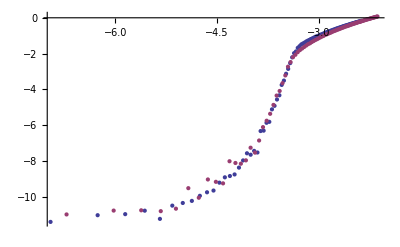

```mathematica
ga10k1=gap10v9[[All,1]];
ga50k1=gap40v9[[All,1]];
ga10k2=gap10v9[[All,2]];
ga50k2=gap40v9[[All,2]];
n1=10;
n2=40;
val=1000;
For[d0=0.063,d0<=0.068,d0+=0.0001,
For[α=0.01,α≤0.8,α+=0.01,
z=α;
j=1;
While[ga10k1[[j]]<=d0,j++];
k=1;
While[ga50k1[[k]]<=d0,k++];
g10k=Table[{Log[ga10k1[[i]]-d0]+z*Log[n1*1000.],
Log[ga10k2[[i]]]+α*Log[n1*1000.]},{i,j,Length[ga10k1]-1}];
g50k=Table[{Log[ga50k1[[i]]-d0]+z*Log[n2*1000.],Log[ga50k2[[i]]]+α*Log[n2*1000.]},{i,k,Length[ga50k1]-1}];
i10=Interpolation[g10k];
i50=Interpolation[g50k];
min=Max[Log[ga10k1[[j]]-d0]+z*Log[n1*1000.],Log[ga50k1[[k]]-d0]+z*Log[n2*1000.]];
max=Min[Log[ga10k1[[Length[ga10k1]-1]]-d0]+z*Log[n1*1000.],Log[ga50k1[[Length[ga50k1]-1]]-d0]+z*Log[n2*1000.]];
delta=(max-min)/50;
int=Sum[delta*(Max[i10[min+k*delta],i50[min+k*delta]]-Min[i10[min+k*delta],i50[min+k*delta]]),{k,0,50}];
If[int<val,
val=int;
d0f=d0;
αf=α;
zf=z;]

]
]


" = val"  val
" = d0" d0f
" = α" αf
" = z" zf
g10k=Table[{Log[ga10k1[[i]]-d0f]+zf*Log[n1*1000.],
Log[ga10k2[[i]]]+αf*Log[n1*1000.]},{i,1,Length[ga10k1]}];
g50k=Table[{Log[ga50k1[[i]]-d0f]+zf*Log[n2*1000.],Log[ga50k2[[i]]]+αf*Log[n2*1000.]},{i,1,Length[ga50k1]}];
ListPlot[{g10k,g50k}]
```

0.634  = d0

0.17  = α

0.17  = z

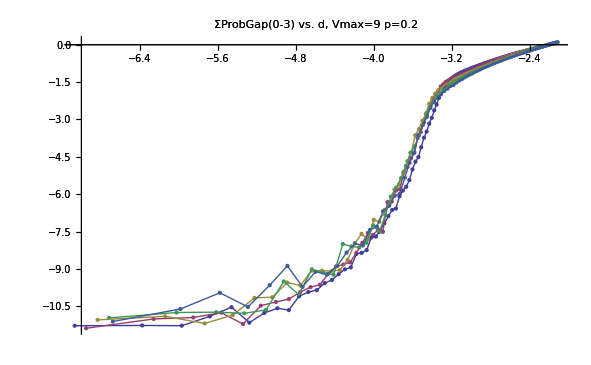

```mathematica
d0f=0.634;
αf=0.17;
zf=0.17;
ga5k1=gap5v9[[All,1]];
ga10k1=gap10v9[[All,1]];
ga20k1=gap20v9[[All,1]];
ga40k1=gap40v9[[All,1]];
ga50k1=gap50v9[[All,1]];
ga5k2=gap5v9[[All,2]];
ga10k2=gap10v9[[All,2]];
ga20k2=gap20v9[[All,2]];
ga40k2=gap40v9[[All,2]];
ga50k2=gap50v9[[All,2]];
g5k=Table[{Log[ga5k1[[i]]-d0f]+zf*Log[5*1000.],
Log[ga5k2[[i]]]+αf*Log[5*1000.]},{i,1,Length[ga5k1]}];
g10k=Table[{Log[ga10k1[[i]]-d0f]+zf*Log[10*1000.],
Log[ga10k2[[i]]]+αf*Log[10*1000.]},{i,1,Length[ga10k1]}];
g20k=Table[{Log[ga20k1[[i]]-d0f]+zf*Log[20*1000.],
Log[ga20k2[[i]]]+αf*Log[20*1000.]},{i,1,Length[ga20k1]}];
g40k=Table[{Log[ga40k1[[i]]-d0f]+zf*Log[40*1000.],
Log[ga40k2[[i]]]+αf*Log[40*1000.]},{i,1,Length[ga40k1]}];
g50k=Table[{Log[ga50k1[[i]]-d0f]+zf*Log[50*1000.],Log[ga50k2[[i]]]+αf*Log[50*1000.]},{i,1,Length[ga50k1]}];
pic1=ListPlot[{g5k,g10k,g20k,g40k,g50k},PlotLabel->"ΣProbGap(0-"<>ngap<>") vs. d, Vmax="<>v<>"  p="<>p,PlotLegend->{"5k","10k","20k","40k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None];
pic2=ListLinePlot[{g5k,g10k,g20k,g40k,g50k},PlotLabel->"ΣProbGap(0-"<>ngap<>") vs. d, Vmax="<>v<>"  p="<>p,PlotLegend->{"5k","10k","20k","40k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None];
" = d0" d0f
" = α" αf
" = z" zf
Show[{pic1,pic2}]
```